22 Ecuaciones diferenciales
22.1 Solución de una ecuación diferencial

Se comprobarán si las funciones en el pdf son solución de las ecuaciones diferenciales correspondientes:

```mathematica
f1[x_]:=7*Exp[x]
f2[x_]:=Cos[x]
f3[x_]:=Sin[x]
f4[x_]:=a*Sin[x]+b*Cos[x]
```

Son solución:

```mathematica
f1'[x]==f1[x]
f2''[x]==-f2[x]
f3''[x]==-f3[x]
f4''[x]==-f4[x]
```

True

True

True

```mathematica
f1'[x]
f2''[x]
f3''[x]
f4''[x]
```

7 ⅇ^x

-Cos[x]

-Sin[x]

-b Cos[x]-a Sin[x]

22.2 Ecuaciones de primer orden

```mathematica
DSolve[y'[x]==y[x],y,x]
```

{{y→Function[{x},ⅇ^x C[1]]}}

Obtengamos la función:

```mathematica
a=DSolve[y'[x]==y[x],y,x][[1,1,2]] (* C[1] es una cte *)
```

Function[{x},ⅇ^x C[1]]

```mathematica
b=DSolve[y'[x]==2*x+3*y[x],y,x][[1,1,2]]
```

Function[{x},2 (-1/9-x/3)+ⅇ^(3 x) C[1]]

22.3 Ecuaciones de mayor orden

```mathematica
DSolve[y''[x]==y[x],y,x](* C[1] es la primera cte, C[2] es la segunda cte *)
DSolve[x^2*y''[x]+x*y'[x]+(x^2-9)*y[x]==0,y,x]
DSolve[x^2*y''[x]+x*y'[x]+(x^2-9)*y[x]==0,y,x]//TraditionalForm
```

{{y→Function[{x},ⅇ^x C[1]+ⅇ^-x C[2]]}}

{{y→Function[{x},BesselJ[3,x] C[1]+BesselY[3,x] C[2]]}}

{{y→({x}↦c_1 3x+c_2 3x)}}

22.4 Ecuaciones con valor inicial

```mathematica
f=DSolve[{y'[x]==y[x],y[0]==3},y,x][[1,1,2]]
```

Function[{x},3 ⅇ^x]

```mathematica
f[x]
f[0]
```

3 ⅇ^x

3

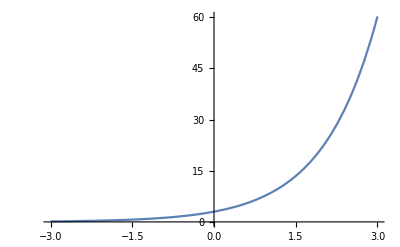

```mathematica
Plot[f[x],{x,-3,3}]
```

```mathematica
g=DSolve[{y''[x]==y[x],y[3]==4,y'[0]==2},y,x][[1,1,2]]
```

Function[{x},(2 ⅇ^-x (2 ⅇ^3-ⅇ^6+ⅇ^(2 x)+2 ⅇ^(3+2 x)))/(1+ⅇ^6)]

```mathematica
g[x]
g[3]//Simplify
g'[0]//Simplify
```

(2 ⅇ^-x (2 ⅇ^3-ⅇ^6+ⅇ^(2 x)+2 ⅇ^(3+2 x)))/(1+ⅇ^6)

4

2

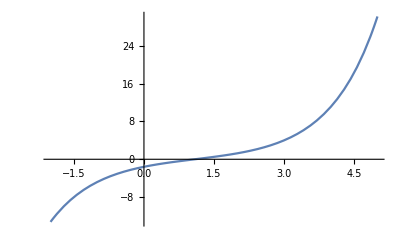

```mathematica
Plot[g[x],{x,-2,5}]
```

22.5 Campo vectorial asociado a la ecuación

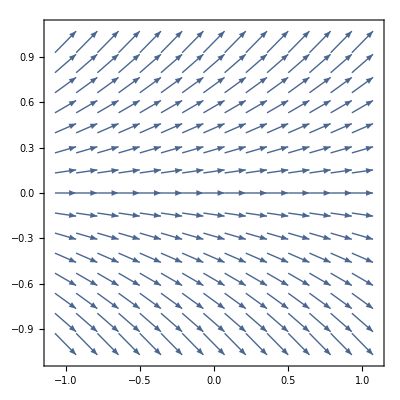

```mathematica
b=VectorPlot[{1,y},{x,-1,1},{y,-1,1}]
```

```mathematica
f=DSolve[{y'[x]==y[x],y[0]==1},y,x][[1,1,2]]
```

Function[{x},ⅇ^x]

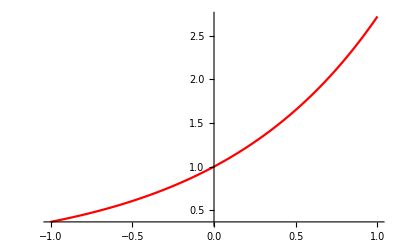

```mathematica
a=Plot[f[x],{x,-1,1},PlotStyle->Red]
```

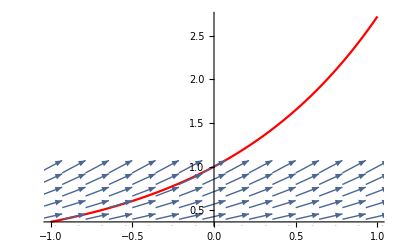

```mathematica
Show[a,b]
```

22.6 Sistemas de ecuaciones diferenciales

```mathematica
DSolve[{x'[t]==t,y'[t]==t^2},{x,y},t]
```

{{x→Function[{t},t^2/2+C[1]],y→Function[{t},t^3/3+C[2]]}}

```mathematica
DSolve[{x'[t]==t,y'[t]==t^2,x[0]==1,y[2]==3},{x,y},t]
```

{{x→Function[{t},1/2 (2+t^2)],y→Function[{t},1/3 (1+t^3)]}}

22.7 Resolución numérica

Se tiene que dar el intervalo para el cual la solución estará definida, así como condiciones iniciales para que no se arroje el mensaje de error.

```mathematica
NDSolve[y'[x]==y[x],y,{x,0,2Pi}]
```

NDSolve[y'[x]==y[x],y,{x,0,2 π}]

```mathematica
NDSolve[{y'[x]==y[x],y[0]==1},y,{x,0,2Pi}]
```

{{y→InterpolatingFunction[…]}}

```mathematica
f[0]
f[-2] (* No está definida en el intervalo dado *)
```

1

1/ⅇ^2

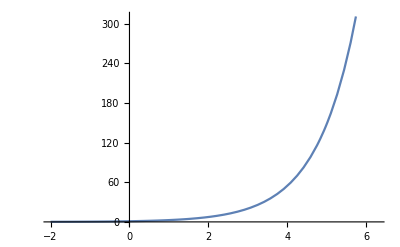

```mathematica
Plot[f[x],{x,-2,2Pi}]
```